This notebook imports dat files, and plots energy eigenvalues and LDoS of projected QAHI

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
datFileEnergylocation="/data/hstci/energies/";
datFileLDOSlocation="/data/hstci/LDOS/";
datfilePBCName="t0=1.0_t=1.0_t_prime=1.5_m_0=-3.0_x_periodic=1_y_periodic=1_L=120_m=0.6666666666666666_c1=4_c2=18";
datfileOBCName="t0=1.0_t=1.0_t_prime=1.5_m_0=-3.0_x_periodic=0_y_periodic=0_L=120_m=0.6666666666666666_c1=4_c2=18";
```

```mathematica
StringJoin[datFileEnergylocation,datfilePBCName];
```

```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyPBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfilePBCName,".csv"]]];
```

```mathematica
dataEnergyOBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".csv"]]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,Dimensions[dataEnergyOBC][[1]]/2}];
```

```mathematica
largestX = Dimensions[Lattice][[1]]
```

1720

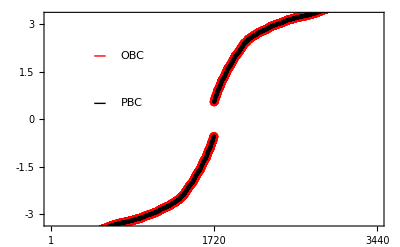

```mathematica
plt1=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,2*largestX},{-3.25,3.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-3,-1.5,0,1.5,3},None},{{1,largestX,2*largestX},None}},BaseStyle-> 18],

ListPlot[dataEnergyPBC,PlotStyle-> {Black,PointSize[0.007]}],

Plot[2.0,{x,0.5*largestX-400,0.5*largestX-280},PlotStyle-> {Thick,Red}],
Plot[0.5,{x,0.5*largestX-400,0.5*largestX-280},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["OBC",{0.5*largestX,2.0}],Inset["PBC",{0.5*largestX,0.5}]}
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".pdf"],plt1];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataLDoSPBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfilePBCName,".csv"]]];
```

```mathematica
dataLDoSPBC=Table[{nn,0,dataLDoSPBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
dataLDoSOBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".csv"]]];
```

```mathematica
dataLDoSOBC=Table[{nn,0,dataLDoSOBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
Dimensions[dataLDoSOBCdat]
```

{1720}

```mathematica
largestX
```

1720

```mathematica
rngOld={0,Max[#]}&@dataLDoSOBC[[All,3]]
```

{0,0.00375113}

```mathematica
rng={0,0.056}
```

{0,0.056}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"0.028"},{rng[[2]]-10^-3,"0.056"}}]
```

```mathematica
(** Crop the image appropriately and put the numbers in inkscape **)
```

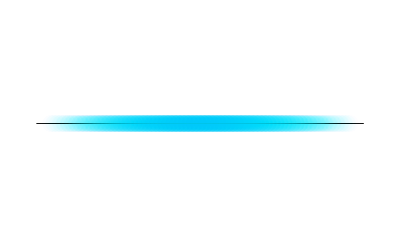

```mathematica
plt2=Show[
ListPlot[Lattice,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {All,{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@dataLDoSOBC,
BaseStyle-> 18
]

]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".pdf"],plt2];
```